```mathematica
ClearAll["Global`*"]

zms = Import[NotebookDirectory[]<>"zms.mx"];
wvals = Import[NotebookDirectory[]<>"wvals.mx"];
Frhos = Import[NotebookDirectory[]<>"Frhos.mx"];
ma1s = Import[NotebookDirectory[]<>"ma1vaues.mx"];
fa1s = Flatten[Import[NotebookDirectory[]<>"fa1s.mx"]];
wf = 0.03728945016641873;
```

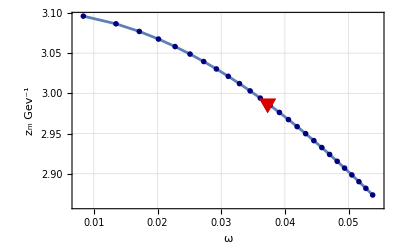

```mathematica
ha = Show[{
ListLinePlot[
Transpose[{wvals,zms 1000}],
Frame->True,
FrameLabel->{Style["ω",Black,15,Bold],Style[Row[{Subscript["z","m"],"  " ,Superscript["Gev","-1"]}],Black,15,Bold]},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->{{Min[wvals] - Min[wvals]/10,Max[wvals] + Min[wvals]/10},{Automatic,Automatic}}
],
ListPlot[Transpose[{wvals,zms 1000}],PlotStyle->Directive[Blend[{Blue,Black},1/2]],PlotMarkers->{{"OpenMarkers",5}}],

ListPlot[{{wf,Interpolation[Transpose[{wvals,zms 1000}]][wf]}},PlotStyle->Directive[Blend[{Red,Black},1/7]],
PlotMarkers->{{"▼",20}}]
}]
```

```mathematica
Export[NotebookDirectory[]<>"wvszm.pdf",ha,ImageResolution->500]
```

C:\Users\Nabeel Thahir\Desktop\Major Project\Publication Code\Model A\wvszm.pdf

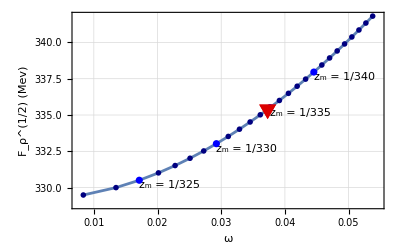

```mathematica
ha = Show[{
ListLinePlot[
Transpose[{wvals,Frhos}],
Frame->True,
FrameLabel->{Style["ω",Black,15,Bold],Style[Row[{Superscript[Subscript["F","ρ"],"1/2"] ," ","(Mev)"}],Black,15,Bold]},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->{{Min[wvals] - Min[wvals]/10,Max[wvals] + Min[wvals]/10},{Automatic,Automatic}}
],
ListPlot[Transpose[{wvals,Frhos}],PlotMarkers->{{"OpenMarkers",5}},PlotStyle->Directive[Blend[{Blue,Black},1/2]]],
Graphics[
Table[
Text[
Row[{Subscript["z","m"]," = ",zms[[i]]}],{wvals[[i]],Frhos[[i]]},{-1,1.3}]
,{i,3,Length[wvals]-5,5} ]],
ListPlot[
Table[
{wvals[[i]],Frhos[[i]]}
,{i,3,Length[wvals]-5,5} ],PlotStyle->Directive[Blue]],

ListPlot[{{wf,Interpolation[Transpose[{wvals,Frhos}]][wf]}},PlotStyle->Directive[Blend[{Red,Black},1/7]],PlotMarkers->{{"▼",20}}]
}]
```

```mathematica
Export[NotebookDirectory[]<>"wvsFrho.pdf",ha,ImageResolution->500]
```

C:\Users\Nabeel Thahir\Desktop\Major Project\Publication Code\Model A\wvsFrho.pdf

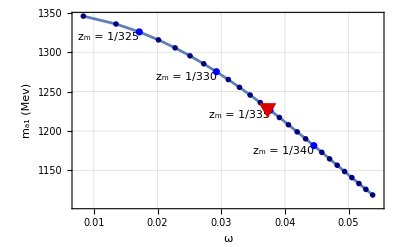

```mathematica
ha = Show[{

ListLinePlot[
Transpose[{wvals,ma1s}],
Frame->True,
FrameLabel->{Style["ω",Black,15,Bold],Style[Row[{Subscript["m","a1"]," ","(Mev)"}],Black,15,Bold]},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->{{Min[wvals] - Min[wvals]/10,Max[wvals] + Min[wvals]/10},{Automatic,Automatic}}
],

ListPlot[Transpose[{wvals,ma1s}],PlotMarkers->{{"OpenMarkers",5}},PlotStyle->Directive[Blend[{Blue,Black},1/2]]],
Graphics[
Table[
Text[
Row[{Subscript["z","m"]," = ",zms[[i]]}],{wvals[[i]],ma1s[[i]]},{1,1.3}]
,{i,3,Length[wvals]-5,5} ]],

ListPlot[
Table[
{wvals[[i]],ma1s[[i]]}
,{i,3,Length[wvals]-5,5} ],PlotStyle->Directive[Blue]],

ListPlot[{{wf,Interpolation[Transpose[{wvals,ma1s}]][wf]}},PlotStyle->Directive[Blend[{Red,Black},1/7]],PlotMarkers->{{"▼",20}}]
}]
```

```mathematica
Export[NotebookDirectory[]<>"wvsma1.pdf",ha,ImageResolution->500]
```

C:\Users\Nabeel Thahir\Desktop\Major Project\Publication Code\Model A\wvsma1.pdf

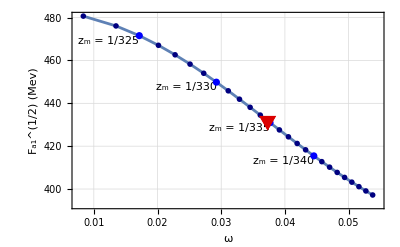

```mathematica
ha = Show[{
ListLinePlot[
Transpose[{wvals,fa1s}],
Frame->True,
FrameLabel->{Style["ω",Black,15,Bold],Style[Row[{Superscript[Subscript["F","a1"],"1/2"]," ","(Mev)"}],Black,15,Bold]},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->{{Min[wvals] - Min[wvals]/10,Max[wvals] + Min[wvals]/10},{Automatic,Automatic}}
],

ListPlot[Transpose[{wvals,fa1s}],PlotMarkers->{{"OpenMarkers",5}},PlotStyle->Directive[Blend[{Blue,Black},1/2]]],
Graphics[
Table[
Text[
Row[{Subscript["z","m"]," = ",zms[[i]]}],{wvals[[i]],fa1s[[i]]},{1,1.3}]
,{i,3,Length[wvals]-5,5} ]],

ListPlot[
Table[
{wvals[[i]],fa1s[[i]]}
,{i,3,Length[wvals]-5,5} ],PlotStyle->Directive[Blue]],

ListPlot[{{wf,Interpolation[Transpose[{wvals,fa1s}]][wf]}},PlotStyle->Directive[Blend[{Red,Black},1/7]],PlotMarkers->{{"▼",20}}]
}]
```

```mathematica
Export[NotebookDirectory[]<>"wvsfa1.pdf",ha,ImageResolution->500]
```

C:\Users\Nabeel Thahir\Desktop\Major Project\Publication Code\Model A\wvsfa1.pdf